## Project : Space Craft / Rocket Hovering

This is 454 final project written by Titipat Achakulvisut.
- We simulate the rocket hovering over x-axis while maintaining y-axis and it’s direction θ(t)

The program contains 2 parts:
1. Optimization Algorithm (takes up to 10-15 minutes to run until the it end of the optimization)
- Note that I use appropriate constant step size in optimization loop before using Armijo to obtain fine result of signal
- We can abort the optimization if it seems to converge at the end (e.g. you can observe that it converges around iteration = 18)
- I let the simulation stop at iteration 18 which gives pretty decent result.

2. Animation Part (takes 1-2 seconds to run)
- Do animation of the hovering rocket

## Optimization Part

```mathematica
Quit[];
```

```mathematica
Off[NIntegrate::"slwcon"];Off[NIntegrate::"ncvb"];
(*NUMBER OF STATE, INITCON*)
NS = 6;  (*# of states*)
x0 = {0,0,-Pi/10,0,0,0}; (*Initial condition*)
T = 25; (*Final time*)
xlen = Length[x0]; (*number of states*)
ulen = 2; (*number of control signal*)

(*Armijo Parameter*)
α = 0.35;
β = 0.5;
γ = β; (*just assign it first*)
iter =1;
maxiter = 20;

(*WEIGHT MATRIX OF COST*)
(*Weight Constant for P Matrix, original cost*)
Q = DiagonalMatrix[{100,30,30,1,1,1}];
R = DiagonalMatrix[{0.1,0.1}];
P1 = DiagonalMatrix[{100,30,30,1,1,1}];
(*Weight Constant for Descent Direction*)
Qn =IdentityMatrix[xlen];
Rn = IdentityMatrix[ulen];
P1n = IdentityMatrix[xlen];
(*Weight for K(t)*)
Qr = IdentityMatrix[xlen];
Rr =  IdentityMatrix[ulen];
P1r = IdentityMatrix[xlen];

(*Desire Trajectory*)
(*xd[t_]:=Piecewise[{{0,t<1},{1*(t-1),1≤t<10},{9,5≤t<T}},0];*)
(*yd[t_]:=Piecewise[{{2.5,t<1},{-0.5*(t-1)+2.5,1≤t<6},{0,6≤t<T}},0];*)
xd[t_]:=Piecewise[{{0,t<5},{10,5≤t<T/2},{0,20≤t<T}},0];
yd[t_]:=Piecewise[{{0,t<5},{0,5≤t<T/2},{0,20≤t<T}},0];
θd[t_]:=Piecewise[{{0,t<1},{0,1≤t<5},{0,5≤t<T}},0];
(*No desired trajectory in state*)
Xd = {xd[t],yd[t],θd[t],0,0,0};

(*STATES AND CONTROLS*)
(*define state as {x[t],y[t],θ[t],x'[t],y'[t],θ'[t]} *)
X = Table[{x[i][t]},{i,1,xlen}];
U = Table[{u[i][t]},{i,1,ulen}];

(*DYNAMICS and its CONSTANT*)
M = 11.2;
gr = 0.28;
Jm = 0.0462;
ra = 0.156;
d = 0.1;
ρ = 1.2;
S = 0.61;
Dr = (1/2)*ρ*S*((x[4][t])^2+(x[5][t])^2);
f = {{x[4][t]},{x[5][t]},{x[6][t]},
{(1/M)*(-M*gr*Sin[x[3][t]]-d*x[4][t]+u[1][t]*Cos[x[3][t]]-u[2][t]*Sin[x[3][t]] )},
{(1/M)*(M*gr*(Cos[x[3][t]]-1)-d*x[5][t]+u[1][t]*Sin[x[3][t]]+u[2][t]*Cos[x[3][t]])},
{(ra/Jm)*u[1][t]}};

(*FUNCTION TO SOLVE ALL EQUATION*)
(*Finding the cost function*)
J[xsol_,usol_]:=(1/2)*NIntegrate[((xsol-Xd).Q.(xsol-Xd))+(usol.R.usol),{t,0,T},Method->{Automatic,"SymbolicProcessing"-> False}]+(1/2)*((xsol-Xd).P1.(xsol-Xd))/.t-> T
(*Directional cost*)
DJ[xsol_,zsol_,usol_,vsol_]:=NIntegrate[Q.(xsol-Xd).zsol + R.usol.vsol,{t,0,T},Method->{Automatic,"SymbolicProcessing"-> False}]+(P1.(xsol-Xd).zsol)/.t-> T
(*Solving Riccati Equation*)
Ric[AA_,BB_,QQ_,RR_,P1_]:= Module[{PMat,RicEq},
PMat = Table[P[i][j][t],{i,1,NS},{j,1,NS}];
RicEq = Transpose[AA].PMat + PMat.AA - PMat.BB.Inverse[RR].Transpose[BB].PMat + QQ;
PMat/.NDSolve[Flatten[Table[{-P[i][j]'[t]== RicEq[[i,j]],P[i][j][T]== P1[[i,j]]},{i,1,NS},{j,1,NS}]],Flatten[PMat],{t,0,T}][[1]]
];

REqSolve[AA_,BB_,QQ_,RR_,PP_,P1_,Xd_,xsol_,usol_]:=Module[{rmat,REq,solr,rsol},
rmat = Table[{r[i][t]},{i,1,xlen}];
REq = (AA-BB.Inverse[RR].BBᵀ.PP)ᵀ.rmat+QQᵀ.(xsol-Xd) - PP.BB.Inverse[RR].RR.usol;
solr = NDSolve[Flatten[Table[{Thread[-r[i]'[t]== REq[[i]]],r[i][T]== (P1.(xsol-Xd)/.t-> T)[[i]]},{i,1,xlen}]],Flatten[rmat],{t,0,T}];
rsol = rmat/.solr[[1]];
Flatten[rsol]
]

(*Finding Descent Direction*)
DescentDir[AA_,BB_,QQ_,RR_,rsol_,Psol_,usol_]:=Module[{v,dynamz,initconz,EqZ,solz,ztraj,vtraj,Z},
Z = Table[{z[i][t]},{i,1,xlen}];;
v = (-Inverse[RR].BBᵀ.Psol.Flatten[Z]-Inverse[RR].BBᵀ.rsol - Inverse[RR].RR.usol);
dynamz = Table[Flatten[D[Z,t]][[i]]== Thread[Flatten[AA.Z+BB.v][[i]]],{i,1,xlen}];
initconz = Thread[Flatten[Z/.t-> 0]== Flatten[-Inverse[Psol/.t-> 0].(rsol/.t-> 0)]];
EqZ = Join[dynamz,initconz];
solz = NDSolve[EqZ,Flatten[Z],{t,0,T}];
ztraj = Table[Z[[i,1]]/.solz[[1]],{i,1,xlen}];
vtraj= Flatten[v]/.solz[[1]];
{ztraj,vtraj}
]

Armijo[xtraj_,utraj_,zsol_,vsol_]:=Module[
{β,γ,α,n,xold,uold,xnew,unew,FOld,Fnew,Dgζ,linSearchIter,maxiters,gradient},
α = 2*10^-1;
β = 0.8;
n = 1;
γ = β;
(*may be interpcurve here is good...*)
(*{xtraj,utraj}=InterpCurve[xtraj,utraj];*)
{xold,uold} = {xtraj,utraj}; (*get former trajectory*)
{xnew,unew} = {xold+γ*zsol,uold+γ*vsol};
{xnew,unew}= Proj[xnew,unew];
FOld = J[xold,uold];
Dgζ = DJ[xold,zsol,uold,vsol];
Fnew = J[xnew,unew];
Print["FOld = ", FOld, " and Fnew = ", Fnew, " and Dgζ = ", Dgζ];
linSearchIter = 0;
maxiters = 40;
Print["While loop is ",And[Fnew> FOld+α*γ*Dgζ, linSearchIter < maxiters]];
While[And[Fnew> FOld+α*γ*Dgζ, linSearchIter < maxiters],
n++;
γ = β^n;
(*Print["α = ", α, " β = ", β, " γ = ",γ];*)
{xnew,unew} = {xold+γ*zsol,uold+γ*vsol};
{xnew,unew}= Proj[xnew,unew];
(*{xnew,unew}=InterpCurve[xnew,unew];*)
Fnew = J[xnew,unew];
Print["Armijo Iteration = ", linSearchIter, ", Current J = ", Fnew];
linSearchIter++;
];
Print["End Armijo loop"];
(*output the x-trajectory, u-trajectory and gradient*)
{xnew,unew,Dgζ}
]

Proj[αtraj_,μtraj_]:=Module[{Psolr,Kr,dynam,initcon,Eqs,utraj,sol,xsol,Usub},
Psolr = Ric[Asol,Bsol,Qr,Rr,P1r];
Kr = Inverse[Rr].Bsolᵀ.Psolr;
dynam = Table[Flatten[D[X,t]][[i]]== Flatten[f][[i]] ,{i,1,xlen}];
initcon = Thread[Flatten[X/.t-> 0]== Flatten[x0]];
Eqs = Join[dynam,initcon];
(*utraj = μtraj + Kr.(αtraj-Flatten[X]);*)
utraj = μtraj + Kr.(αtraj-(Flatten[X]));
(*substitute table*)
Usub = Table[U[[i,1]]-> utraj[[i]],{i,1,ulen}];
sol = NDSolve[Eqs/.Usub,Flatten[X],{t,0,T}];
xsol =  Table[X[[i,1]]/.sol[[1]],{i,1,xlen}];
{xsol,utraj/.sol[[1]]}
]

InterpCurve[xtraj_,utraj_]:=Module[{dt,interpx1,interpx2,interpx3,interpx4,interpx5,interpx6,interpu1,interpu2,interpxnew,interpunew},
dt = 0.05;
interpx1 = Table[{τ,xtraj[[1]]/.t-> τ},{τ,0,T,dt}];
interpx2 = Table[{τ,xtraj[[2]]/.t-> τ},{τ,0,T,dt}];
interpx3 = Table[{τ,xtraj[[3]]/.t-> τ},{τ,0,T,dt}];
interpx4 = Table[{τ,xtraj[[4]]/.t-> τ},{τ,0,T,dt}];
interpx5 = Table[{τ,xtraj[[5]]/.t-> τ},{τ,0,T,dt}];
interpx6 = Table[{τ,xtraj[[6]]/.t-> τ},{τ,0,T,dt}];
interpu1= Table[{τ,utraj[[1]]/.t-> τ},{τ,0,T,dt}];
interpu2= Table[{τ,utraj[[2]]/.t-> τ},{τ,0,T,dt}];
interpxnew = {Interpolation[interpx1,InterpolationOrder->2][t],
Interpolation[interpx2,InterpolationOrder->2][t],
Interpolation[interpx3,InterpolationOrder->2][t],
Interpolation[interpx4,InterpolationOrder->2][t],Interpolation[interpx5,InterpolationOrder->2][t],
Interpolation[interpx6,InterpolationOrder->2][t]};
interpunew = {Interpolation[interpu1,InterpolationOrder->2][t],
Interpolation[interpu2,InterpolationOrder->2][t]};
{interpxnew,interpunew}
]

(*Linearized Dynamics x'= Ax+Bu*)
A = D[Flatten[f],Xᵀ];
B = D[Flatten[f],Uᵀ];

(*Compute the first feasible solution set*)
utest = {U[[1,1]]-> 0,U[[2,1]]-> 0}; (*test control using set control to zero*)

(*Compute the dynamics*)
dynam = Table[Flatten[D[X,t]][[i]]== Flatten[f][[i]] ,{i,1,xlen}];
initcon = Thread[Flatten[X/.t-> 0]== Flatten[x0]];
Eqs = Join[dynam,initcon];
sol = NDSolve[Eqs/.utest,Flatten[X],{t,0,T}];

(*First Linearize DYNAMICS*)
xsol = Table[X[[i,1]]/.sol[[1]],{i,1,xlen}];
usol = {xsol[[1]],xsol[[1]]};
(*Matrix containing dynamics*)
Asol = A/.sol[[1]]/.utest;
Bsol = B/.sol[[1]]/.utest;
(*Riccati Equation P(t) and r(t)*)
Psol = Ric[Asol,Bsol,Q,R,P1];
rsol = REqSolve[Asol,Bsol,Q,R,Psol,P1,Xd,xsol,usol];
{zsol,vsol}=DescentDir[Asol, Bsol, Q, R, rsol, Psol, usol];

(*first trajcetory*)
{xtraj,utraj}={xsol,usol};
(*clear unused variable*)
Clear[xsol,usol,sol];
(*Interpolating function*)
(*Norm of gradient*)
δ = Norm[DJ[xtraj,zsol,utraj,vsol]]; 

Print["Initial Cost is ", J[xtraj,utraj]];
Print["Initial Direction DJ is ", DJ[xtraj,zsol,utraj,vsol], "(hope to get minus - if not please contact me!)"];
Print["Let Start the Optimization Loop!"];

(*** OPTIMIZATION ITERATION ***)
(*initial of iteration*)
iter = 1;
maxiter = 18;
While[(iter≤ maxiter && Abs[δ]>0.05),
(*obtain linearize dynamics*)
Xsub = Table[X[[i,1]]-> xtraj[[i]],{i,1,xlen}];
Usub = Table[U[[i,1]]-> utraj[[i]],{i,1,ulen}];
Asol = A/.Xsub/.Usub;
Bsol = B/.Xsub/.Usub;
(*Solving Riccati Equation, r(t) equation*)
Psol = Ric[Asol,Bsol,Q,R,P1];
rsol = REqSolve[Asol,Bsol,Q,R,Psol,P1,Xd,xtraj,utraj];
{zsol,vsol}=DescentDir[Asol, Bsol, Q, R, rsol, Psol, utraj]; (*note here*)

(*Update rule using Constant Step Size + Armijo*)
If[iter≤14,
{xtraj,utraj} = Proj[xtraj+α*γ*zsol,utraj+α*γ*vsol],
{xtraj,utraj,δ} = Armijo[xtraj,utraj,zsol,vsol];
];
(*Projection and interpolation*)
{xtraj,utraj}=InterpCurve[xtraj,utraj];

(*Print Cost and Update the iteration*)
Print["Cost of Iteration # ",iter," is ",J[xtraj,utraj] ];
iter++;
]
```

Initial Cost is 207115.

Initial Direction DJ is -404732.(hope to get minus - if not please contact me!)

Let Start the Optimization Loop!

Cost of Iteration # 1 is 215196.

Cost of Iteration # 2 is 146788.

## Animation Part

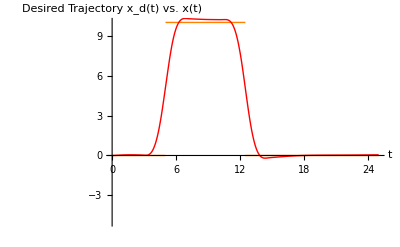

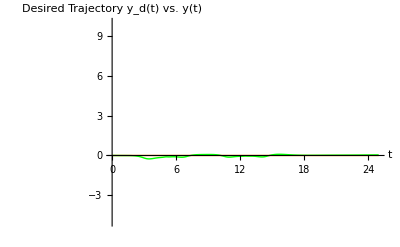

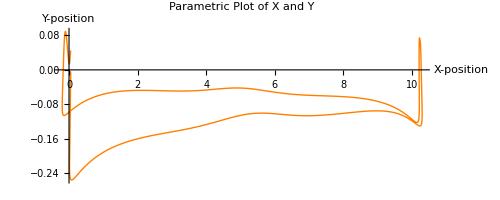

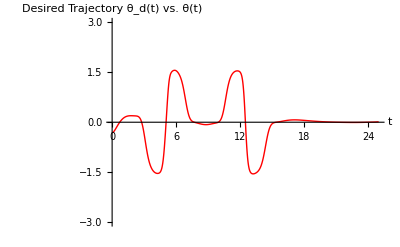

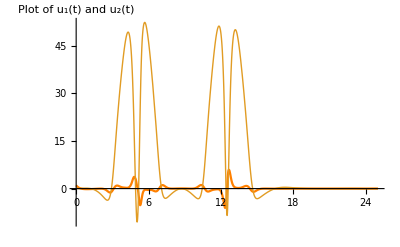

```mathematica
(*Run this part directly after optimization section, don't need to Quit!*)

(*ALL PLOTS*)
Show[
{Plot[{Xd[[1]]},{t,0,T},PlotStyle->{Orange,Thick},
LabelStyle->{(FontFamily-> "Helvetica"),FontSize-> 14}],
Plot[{xtraj[[1]]},{t,0,T},
PlotStyle->{Thick,Red},LabelStyle->{(FontFamily-> "Helvetica"),FontSize-> 14}]
},
AxesLabel->{"t","Desired Trajectory x_d(t) vs. x(t)"},
PlotRange->  {{0,T},{-5,10}}
]

Show[
{Plot[{Xd[[2]]},{t,0,T},PlotStyle->{Orange,Thick},
LabelStyle->{(FontFamily-> "Helvetica"),FontSize-> 14}],
Plot[{xtraj[[2]]},{t,0,T},
PlotStyle->{Thick,Green},LabelStyle->{(FontFamily-> "Helvetica"),FontSize-> 14}]
},
AxesLabel->{"t","Desired Trajectory y_d(t) vs. y(t)"},
PlotRange-> {{0,T},{-5,10}}
]

ParametricPlot[{xtraj[[1]],xtraj[[2]]},{t,0,T},PlotStyle->{Orange,Thick},
LabelStyle->{(FontFamily-> "Helvetica"),FontSize-> 14},AxesLabel->{"X-position","Y-position"},
PlotRange->Full,
PlotLabel->"Parametric Plot of X and Y"]

Plot[{xtraj[[3]]},{t,0,T},
PlotStyle->{Thick,Red},LabelStyle->{(FontFamily-> "Helvetica"),FontSize-> 14},
AxesLabel->{"t","Desired Trajectory θ_d(t) vs. θ(t)"},
PlotRange->{{0,T},{-3,3}}]

Plot[{utraj[[1]],utraj[[2]]},{t,0,T},PlotStyle->{Orange,Thick},
LabelStyle->{(FontFamily-> "Helvetica"),FontSize-> 14},PlotRange->Full,
AxesLabel->"Plot of u_1(t) and u_2(t)"]

ω = {{0,-1},{1,0}};
Rot[θ_] := MatrixExp[θ ω];
p[x_,y_] := {x,y};
g[x_,y_,θ_] := Join[Join[Rot[θ],Transpose[{p[x,y]}],2],{{0,0,1}}];

(*Drawing Regtangle Function, using function from last homework*)
Hom[point_]:= Flatten[{point,1}];
UnHom[point_]:= {point[[1]],point[[2]]}
Rect = {{0.2,0.5},{0.2,-0.5},{-0.2,-0.5},{-0.2,0.5}};
Triang = {{0.2,0.5},{0,0.9},{-0.2,0.5}};
Fire = {{0.2,-0.5},{0.2,-0.8},{0.1,-0.6},{0,-0.8},{-0.1,-0.6},{-0.2,-0.8},{-0.2,-0.5}};
Rectfunc[x_,y_,θ_]:= Map[UnHom,Transpose[g[x,y,θ].Transpose[Map[Hom,Rect]]]]
Triangfunc[x_,y_,θ_]:= Map[UnHom,Transpose[g[x,y,θ].Transpose[Map[Hom,Triang]]]]
Firefunc[x_,y_,θ_]:= Map[UnHom,Transpose[g[x,y,θ].Transpose[Map[Hom,Fire]]]]

(*note that function g is declared from above*)
Rectdraw[x_,y_,θ_]:= Graphics[{Thick,Gray, 
Line[{Rectfunc[x,y,θ][[1]],Rectfunc[x,y,θ][[2]]}],
Line[{Rectfunc[x,y,θ][[2]],Rectfunc[x,y,θ][[3]]}],
Line[{Rectfunc[x,y,θ][[3]],Rectfunc[x,y,θ][[4]]}],
Line[{Rectfunc[x,y,θ][[4]],Rectfunc[x,y,θ][[1]]}]
}]
Triandraw[x_,y_,θ_]:=Graphics[{Thick,Gray,
Line[{Triangfunc[x,y,θ][[1]],Triangfunc[x,y,θ][[2]]}],
Line[{Triangfunc[x,y,θ][[2]],Triangfunc[x,y,θ][[3]]}]
}]
Firedraw[x_,y_,θ_]:= Graphics[{Thick,Red, 
Line[{Firefunc[x,y,θ][[1]],Firefunc[x,y,θ][[2]]}],
Line[{Firefunc[x,y,θ][[2]],Firefunc[x,y,θ][[3]]}],
Line[{Firefunc[x,y,θ][[3]],Firefunc[x,y,θ][[4]]}],
Line[{Firefunc[x,y,θ][[4]],Firefunc[x,y,θ][[5]]}],
Line[{Firefunc[x,y,θ][[5]],Firefunc[x,y,θ][[6]]}],
Line[{Firefunc[x,y,θ][[6]],Firefunc[x,y,θ][[7]]}]
}]

x[τ_]:= xtraj[[1]]/.t-> τ
y[τ_]:= xtraj[[2]]/.t-> τ
θ[τ_]:= xtraj[[3]]/.t-> τ
star = RandomReal[{-5,15},{40,2}];
rocketmovie= Animate[
Show[
{Rectdraw[x[τ],y[τ],θ[τ]],
Triandraw[x[τ],y[τ],θ[τ]],
Firedraw[x[τ],y[τ],θ[τ]],
ListPlot[star,PlotStyle->{Yellow,PointSize[Large]}]
(*Graphics[{Thick,Green,Line[{{-40,-3},{40,-3}}]}]*)
}
, AspectRatio -> Automatic, PlotRange -> {{-3,12},{-5,5}},
Background->LightBlue
],{τ,0,T }, AnimationRate->1
]
```

### Export the movie code (but frame rate is really bad)

```mathematica
Export["rocket.mov",rocketmovie]
```

rocket.mov